```mathematica
Quit
```

The notebook presents the computation of the spin corrections to the partial amplitudes and fluxes in the Hamilton-Jacobi formalism. See arXiv:2410.05769 (https://arxiv.org/abs/2410.05769v1 )
Specifically, it includes:
- examples on how to use the package SpinOrbitsHamiltonJacobi,
- examples on how to use the package TeukolskySpinFluxesHamiltonJacobi
- comparisons with the results of Skoupý et at, PRD 108, 044041 (https://journals.aps.org/prd/abstract/10.1103/PhysRevD.108.044041 )
- computation of the corrections due spin precession on the asymptotic partial amplitudes
- computation of waveform snaphots
- some convergence tests of the amplitudes and fluxes in terms of the Fourier harmonics modes in the orbits  (see the “Convergence tests” chapter)

PREREQUISITEs: the following packages are needed
-  SpinOrbitsHamiltonJacobi
- SpinOrbitsHamiltonJacobiNoChop (see the “Convergence tests” chapter)
- TeukolskySpinFluxesHamiltonJacobi (developed with contributions from the code of PRD 108, 044041 (https://journals.aps.org/prd/abstract/10.1103/PhysRevD.108.044041 ) )
- Teukolsky and KerrGeodesics from the BPToolkit. These package are only needed for testing, and are not required by TeukolskySpinFluxesHamiltonJacobi
- a modified version of the SpinWeightedSpheroidalHarmonics from the BPToolkit (https://zenodo.org/records/8091168 ) . The mod was developed in  (https://journals.aps.org/prd/abstract/10.1103/PhysRevD.108.044041 )
  To load it properly, make sure that mod_SpinWeightedSpheroidalHarmonics2 has the same version number or higher compare to the vanilla SpinWeightedSpheroidalHarmonics package. The version can be checked in PacletInfo.wl contain inside the folder “mod_SpinWeightedSpheroidalHarmonics2”. To update the version of the mod_SpinWeightedSpheroidalHarmonics2 , open PacletInfo.wl , increase the number in “Version”, then run the command PacletDataRebuild[]

```mathematica
(*PacletDataRebuild[]*)
```

If you make use of this notebook, please acknowledge 
- "Piovano, Pantelidou, Mac Uilliam and Witzany“ arXiv:2410.05769 (https://arxiv.org/abs/2410.05769v1 )
- “Piovano, Brito, Maselli, Pani” PRD 104, 124019 (https://journals.aps.org/prd/abstract/10.1103/PhysRevD.104.124019 )
-  “Skoupý, Lukes-Gerakopoulos, Drummond, Hughes” PRD 108, 044041 (https://journals.aps.org/prd/abstract/10.1103/PhysRevD.108.044041 )
- SpinWeightedSpheroidalHarmonics package, version 0.3.0 (https://zenodo.org/records/8091168 ) of the  BHPToolkit (https://bhptoolkit.org/ )
- Teukolsky package, (https://zenodo.org/records/10040501) of the  BHPToolkit
- KerrGeodesics package,  (https://zenodo.org/records/8108265) of the  BHPToolkit

### Convention for EoM

Here we follow the same convention of  CQG, Volume 37, Number 14  (https://iopscience.iop.org/article/10.1088/1361-6382/ab79d5 )

r_1== p/(1-e)
r_2== p/(1+e)
z_1==√(1-x^2)

or

p==2(r_1 r_2)/(r_1+r_2)
e== (r_1-r_2)/(r_1+r_2)
x ==  Sign[ℒ]√(1-z_1^2)

(circular) 0<e<1 (parabolic)
(retrograde) -1 < x < 1 (prograde)
p> p_LSO(e,x)

Equatorial orbits

x==±1
z_1==0
𝒬 ==0

“spar” and “sort” are the parallel and orthogonal component of the spin to the total angular momentum.

### Loading all the necessary files

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
PacletDirectoryLoad["mod_SpinWeightedSpheroidalHarmonics2"];
```

```mathematica
<<SpinWeightedSpheroidalHarmonics`
<<KerrGeodesics`
<<Teukolsky`
```

```mathematica
Get["SpinOrbitsHamiltonJacobi.wl"]
```

```mathematica
Get["TeukolskySpinFluxesHamiltonJacobi.wl"]
```

## Calculation of the orbits

IMPORTANT NOTE: all the functions for the orbits take as input the mean anomalies w_r and w_z. The input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- inclination “x” defined as  x=Sign[L_z]√(1-z_1^2)

It computes the maps between the fixed turning points and fixed constants of motion parametrizations.

```mathematica
AbsoluteTiming[corrDHMapFC=KerrSpinOrbitCorrectionDHMapFC[0.9`45,12`45,0.2`45,√3/2`45,12,12];]
```

{2.10851,Null}

Spin corrections to the orbits - fixed turning points (on average)

```mathematica
AbsoluteTiming[corrDHpar=KerrSpinOrbitCorrectionDHPar[0.9`45,12`45,0.2`45,√3/2`45,12,12];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{10.9143,Null}

Spin corrections to the orbits - fixed constants of motion

```mathematica
AbsoluteTiming[corrFCpar=KerrSpinOrbitCorrectionFCPar[0.9`45,12`45,0.2`45,√3/2`45,12,12];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{11.2533,Null}

The above times can be halved by rewriting the code and sampling only once ξ_r and ξ_z (the slowest part in the code)

Spin corrections to the orbits - orthogonal component of the spin (valid in any parametrization)

```mathematica
AbsoluteTiming[corrort=KerrSpinOrbitCorrectionOrt[0.9`45,12`45,0.2`45,√3/2`45,12,12];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Sampling ξ_r function

Sampling ξ_z function

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{26.1063,Null}

Further speed-up are possible by vectorized some functions in the code.

### Constants of motion and frequencies

```mathematica
{corrDHpar["Eg"],corrDHpar["Lzg"],corrDHpar["Kg"]}
```

{0.9616973197795034007609404866267657572818793,3.26946895953061732307367216562517597552784,9.35729204317729381252747992024611720194722}

```mathematica
{corrDHpar["Es"],corrDHpar["Jzs"],corrDHpar["Ks"]}
```

{-0.000928214181658846856805717944177529149984,0.645243976886216747361970464180263120955,5.591894927656566183392786137720141975263}

Mino-time frequencies. Order of appearance: Υ_t , Υ_r , Υ_z , Υ_ϕ

```mathematica
corrDHpar["MinoFrequenciesGeo"]
```

{174.40311720101345332028293726927914238,3.125479149381515993335855471997374661382,3.7823038523318562539454014838462902011691,3.925708635595162652008678054660876015}

```mathematica
corrFCpar["MinoFrequenciesGeo"]
```

{174.40311720101345332028293726927914238,3.125479149381515993335855471997374661382,3.7823038523318562539454014838462902011691,3.925708635595162652008678054660876015}

BL frequencies. Order of appearance: Ω_t , Ω_r , Ω_z , Ω_ϕ

```mathematica
corrDHpar["BLFrequenciesGeo"]
```

{0.017921005080311453809464401260483808348,0.021687134456274944124239925846286517663,0.02250939489269834238385455377106869716}

```mathematica
corrFCpar["BLFrequenciesGeo"]
```

{0.017921005080311453809464401260483808348,0.021687134456274944124239925846286517663,0.02250939489269834238385455377106869716}

### Oscillating terms geodesic coordinate time and azimuthal trajectories

```mathematica
{corrDHpar[ "Δtrg"][23π/5],corrDHpar[ "Δtzg"][3π/5]}
```

{-20.13818742697151622345443364764157173,-0.00756680284797815327273854618080349465451}

```mathematica
{corrFCpar[ "Δtrg"][23π/5],corrFCpar[ "Δtzg"][3π/5]}
```

{-20.13818742697151622345443364764157173,-0.00756680284797815327273854618080349465451}

```mathematica
{corrDHpar[ "Δϕrg"][23π/5],corrDHpar[ "Δϕzg"][3π/5]}
```

{0.009498703462332319148190139672382625394,-0.0397938698998906586433123086026511751615}

```mathematica
{corrFCpar[ "Δϕrg"][23π/5],corrFCpar[ "Δϕzg"][3π/5]}
```

{0.009498703462332319148190139672382625394,-0.0397938698998906586433123086026511751615}

### Spin corrections parallel component of the spin - fixed turning points (on average)

Mino-time frequencies. Order of appearance: Υ_t , Υ_r , Υ_z , Υ_ϕ

```mathematica
corrDHpar["MinoFrequenciesCorrection"]
```

{-0.2465265997809355326011441563603,0.127886329175585782482987002251263,-0.0579672427315269498777511205281664584,-0.1252293888922623808239395757299158}

BL frequencies. Order of appearance: Ω_t , Ω_r , Ω_z , Ω_ϕ

```mathematica
corrDHpar["BLFrequenciesCorrection"]
```

{0.00075861220685752180259008448839838,-0.0003017193044455729565698364447956,-0.00068622755273518495724606462667317}

#### Spin corrections to the radial and polar trajectories

```mathematica
corrDHpar["δrpar"][3π/4`25,23π/7`25]
```

0.01049060435890409563984

```mathematica
corrDHpar["δzpar"][5π/3`25,23π/14`25]
```

-0.0024234603454970428009425

#### Spin corrections to the radial and polar velocities

```mathematica
corrDHpar["δvrpar"][3π/2`25,23π/5`25]
```

-0.310349654986826307651

```mathematica
corrDHpar["δvzpar"][5π/3`25,23π/14`25]
```

-0.0223322962188529633067

#### Spin corrections to the coordinate time and azimuthal trajectories - purely oscillatory term

```mathematica
corrDHpar["Δδtpar"][3π/2`25,23π/5`25]
```

-0.805590779259434027602059

```mathematica
corrDHpar["Δδϕpar"][3π/2`25,23π/5`25]
```

0.0018589190204809524428104

#### Spin corrections to the coordinate time and azimuthal velocities

```mathematica
corrDHpar["δvtpar"][π/4`25,23π/7`25]
```

-0.32954416148975210486002

```mathematica
corrDHpar["δvϕpar"][π/4`25,23π/7`25]
```

-0.1287090248177304738417

### Spin corrections parallel component of the spin - fixed constants of motion

Mino-time frequencies. Order of appearance: Υ_t , Υ_r , Υ_z , Υ_ϕ

```mathematica
corrFCpar["MinoFrequenciesCorrection"]
```

{-51.6495774253989182551347980084729,-0.9372692637974553501495359837449736,-0.9437460043824355088693635016299163147,-0.9099644366364144147526057949482891}

BL frequencies. Order of appearance: Ω_t , Ω_r , Ω_z , Ω_ϕ

```mathematica
corrFCpar["BLFrequenciesCorrection"]
```

{-0.00006683896794978742072851264590585,0.0010113656721437827414063676122781,0.001448576732614843027626981459052}

#### Spin corrections to the radial and polar trajectories

```mathematica
corrFCpar["δrpar"][3π/4`25,23π/7`25]
```

8.4063208468561948819494

```mathematica
corrFCpar["δzpar"][5π/3`25,23π/14`25]
```

-0.026972203612951115041419

#### Spin corrections to the radial and polar velocities

```mathematica
corrFCpar["δvrpar"][3π/2`25,23π/5`25]
```

-48.0455803615680990945

```mathematica
corrFCpar["δvzpar"][5π/3`25,23π/14`25]
```

-0.61423263381104924978795

#### Spin corrections to the coordinate time and azimuthal trajectories - purely oscillatory term

```mathematica
corrFCpar["Δδtpar"][3π/2`25,23π/5`25]
```

148.073000902745697191586

```mathematica
corrFCpar["Δδϕpar"][3π/2`25,23π/5`25]
```

-0.07283706847115258457752

#### Spin corrections to the coordinate time and azimuthal velocities

```mathematica
corrFCpar["δvtpar"][5π/9`35,23π/7`25]
```

-118.93516890219493629519002

```mathematica
corrFCpar["δvϕpar"][5π/9`35,23π/7`25]
```

-0.86921403525772869038853

### Spin corrections orthogonal component of the spin

Mino-time precession frequency

```mathematica
corrort["MinoPrecessionFrequency"]
```

3.46278194544771203193205896255246449238

BL spin precession frequency

```mathematica
corrort["BLPrecessionFrequency"]
```

0.019855046177050726874620081980084135437

#### Coordinate time and azimuthal velocities

```mathematica
corrort["δvtort"][3π/2,2π/5,π/5]
```

-0.25320932834474057721671683002383

```mathematica
corrort["δvtortplus"][3π/2,2π/5]Exp[-I wp]+corrort["δvtortminus"][3/2π,2π/5]Exp[I wp]/.wp->π/5
```

-0.25320932834474057721671683002383+0. ⅈ

```mathematica
corrort["δvϕort"][3π/2,2π/5,π/5]
```

-0.5124427018478202316413138135562417

```mathematica
corrort["δvϕortplus"][3π/2,2π/5]Exp[-I wp]+corrort["δvϕortminus"][3/2π,2π/5]Exp[I wp]/.wp->π/5
```

-0.5124427018478202316413138135562417+0. ⅈ

#### Coordinate time and azimuthal trajectories

```mathematica
corrort["Δδtort"][3π/2,2π/5,7π/2]
```

-0.16961274974463854112658322215

```mathematica
corrort["Δδtortplus"][3π/2,2π/5]Exp[-I wp]+corrort["Δδtortminus"][3π/2,2π/5]Exp[I wp]/.wp->7π/2
```

-0.16961274974463854112658322215+0. ⅈ

```mathematica
corrort["Δδϕort"][3π/2,2π/5,7π/2]
```

-0.14173635988011204434063860126882

```mathematica
corrort["Δδϕortplus"][3π/2,2π/5]Exp[-I wp]+corrort["Δδϕortminus"][3π/2,2π/5]Exp[I wp]/.wp->7π/2
```

-0.14173635988011204434063860126882+0. ⅈ

#### Radial and polar velocities

```mathematica
corrort["δvrort"][3π/2,23π/5,π/5]
```

0.013322564873647407862064998139415

```mathematica
corrort["δvrortplus"][3π/2,23π/5]Exp[-I wp]+corrort["δvrortminus"][3π/2,23π/5]Exp[I wp]/.wp->π/5
```

0.013322564873647407862064998139415+0. ⅈ

```mathematica
corrort["δvzort"][3π/2,2π/5,π/4]
```

-0.71288646098803666335067248585349018

```mathematica
corrort["δvzortplus"][3π/2,2π/5]Exp[-I wp]+corrort["δvzortminus"][3π/2,2π/5]Exp[I wp]/.wp->π/4
```

-0.71288646098803666335067248585349018+0. ⅈ

#### Radial and polar trajectories

```mathematica
corrort["δrort"][π/2,23π/5,π/5]
```

0.0094174199070941184293744537781334

```mathematica
corrort["δrortplus"][π/2,23π/5,π/5]Exp[-I wp]+corrort["δrortminus"][π/2,23π/5,π/5]Exp[I wp]/.wp->π/5
```

0.0094174199070941184293744537781334+0. ⅈ

```mathematica
corrort["δzort"][3π/2,23π/5,π/5]
```

0.2183442745133754357297837355512311

```mathematica
corrort["δzortplus"][π/2,23π/5,π/5]Exp[-I wp]+corrort["δzortminus"][π/2,23π/5,π/5]Exp[I wp]/.wp->π/5
```

0.2499483257163760725459425833041931+0. ⅈ

### Map between the parametrizations

Mino-time frequencies. Order of appearance: Υ_t , Υ_r , Υ_z , Υ_ϕ

```mathematica
corrDHpar["MinoFrequenciesCorrection"]
```

{-0.2465265997809355326011441563603,0.127886329175585782482987002251263,-0.0579672427315269498777511205281664584,-0.1252293888922623808239395757299158}

```mathematica
corrFCpar["MinoFrequenciesCorrection"]-{corrDHMapFC["freqdevtime"],corrDHMapFC["freqdevrad"],corrDHMapFC["freqdevpol"],corrDHMapFC["freqdevphi"]}
```

{-0.2465265997809355326011849152321,0.127886329175585782482987002251263,-0.0579672427315269498777511205281664584,-0.125229388892262380823939599607947}

#### Spin corrections to the radial and polar trajectories

```mathematica
corrDHpar["δrpar"][3π/4`25,23π/7`25]
```

0.01049060435890409563984

```mathematica
corrFCpar["δrpar"][3π/4`25,23π/7`25]+corrDHMapFC["ηr"][3π/4`25]
```

0.01049060435890409566

```mathematica
corrDHpar["δzpar"][5π/3`25,23π/14`25]
```

-0.0024234603454970428009425

```mathematica
corrFCpar["δzpar"][5π/3`25,23π/14`25]+corrDHMapFC["ηz"][23π/14`25]
```

-0.00242346034549704280069

#### Spin corrections to the radial and polar velocities

```mathematica
corrDHpar["δvrpar"][3π/2`25,23π/5`25]
```

-0.310349654986826307651

```mathematica
corrFCpar["δvrpar"][3π/2`25,23π/5`25]+corrDHMapFC["dδrdλFCmapDH"][3π/2`25]
```

-0.3103496549868263077

```mathematica
corrDHpar["δvzpar"][5π/3`25,23π/14`25]
```

-0.0223322962188529633067

```mathematica
corrFCpar["δvzpar"][5π/3`25,23π/14`25]+corrDHMapFC["dδzdλFCmapDH"][23π/14`25]
```

-0.0223322962188529633071

#### Spin corrections to the coordinate time and azimuthal trajectories - purely oscillatory term

```mathematica
corrDHpar["Δδtpar"][3π/2`25,23π/5`25]
```

-0.805590779259434027602059

```mathematica
corrFCpar["Δδtpar"][3π/2`25,23π/5`25]+corrDHMapFC["ηtrΔδt"][3π/2`25]+corrDHMapFC["ηtzΔδt"][23π/5`25]
```

-0.8055907792594340270537

```mathematica
corrDHpar["Δδϕpar"][3π/2`25,23π/5`25]
```

0.0018589190204809524428104

```mathematica
corrFCpar["Δδϕpar"][3π/2`25,23π/5`25]+corrDHMapFC["ηϕrΔδϕ"][3π/2`25]+corrDHMapFC["ηϕzΔδϕ"][23π/5`25]
```

0.00185891902048095244264

#### Spin corrections to the coordinate time and azimuthal velocities

```mathematica
corrDHpar["δvtpar"][π/4`25,23π/7`25]
```

-0.32954416148975210486002

```mathematica
corrFCpar["δvtpar"][π/4`25,23π/7`25]+corrDHMapFC["ηtr"][π/4`25]+corrDHMapFC["ηtz"][23π/7`25]
```

-0.32954416148975210462

```mathematica
corrDHpar["δvϕpar"][π/4`25,23π/7`25]
```

-0.1287090248177304738417

```mathematica
corrFCpar["δvϕpar"][π/4`25,23π/7`25]+corrDHMapFC["ηϕr"][π/4`25]+corrDHMapFC["ηϕz"][23π/7`25]
```

-0.1287090248177304738421

## Check amplitudes and fluxes - parallel component of the spin

```mathematica
AbsoluteTiming[ampFC=TeukolskySpinModeCorrectionFC[2,1,2,1,corrFCpar];]
```

{4.87806,Null}

```mathematica
AbsoluteTiming[ampDH=TeukolskySpinModeCorrectionDH[2,1,2,1,corrDHpar];]
```

{4.89767,Null}

The above times can be halved by rewriting the code and sampling only once ξ_r and ξ_z (the slowest part in the code)

Further speed-up are possible by vectorized some functions in the code.

```mathematica
ampFC
```

<|l→2,m→1,k→1,n→2,ωg→0.08003853950959619412702328213832283152,ωs→0.0023262644688590509275763237795184,Amplitudes→<|ℐ→-0.00009730865721188220420403297+0.000029673808442272666836528212 ⅈ,ℋ→-0.00010271913842617291632218988-0.000021758169463212581866654938 ⅈ|>,AmplitudesCorrection→<|ℐ→-0.0012954792166749171213692127+0.00039540241212095188490354436 ⅈ,ℋ→-0.0013789693131696349662816446-0.00029226577699267544182745338 ⅈ|>,Fluxes→<|Energy→<|ℐ→1.2856169812884931771322153×10^-7,ℋ→-1.7790028335794433803518218×10^-11|>,AngularMomentum→<|ℐ→1.6062474267591483923817616×10^-6,ℋ→-2.2226827781710714825457448×10^-10|>|>,FluxesCorrection→<|Energy→<|ℐ→3.4158942845443036658498523×10^-6,ℋ→-4.7767030431344259161074631×10^-10|>,AngularMomentum→<|ℐ→0.000042631434170761425000674834,ℋ→-5.9615436818283526077013102×10^-9|>|>,stepsr→64,stepsθ→32|>

```mathematica
ampDH
```

<|l→2,m→1,k→1,n→2,ωg→0.08003853950959619412702328213832283152,ωs→0.000529277556534285691364267905328,Amplitudes→<|ℐ→-0.000097308657198923475762063339+0.000029673808428192811811535853 ⅈ,ℋ→-0.0001027191384259218673108466-0.000021758169462505243914772095 ⅈ|>,AmplitudesCorrection→<|ℐ→7.302651794094279368375137×10^-6-2.146763206854170465226377×10^-6 ⅈ,ℋ→3.740718765524608655046767×10^-6+7.80648550229005844494349×10^-7 ⅈ|>,Fluxes→<|Energy→<|ℐ→1.2856169808714119695005611×10^-7,ℋ→-1.7790028335661539421962934×10^-11|>,AngularMomentum→<|ℐ→1.6062474262380479198004892×10^-6,ℋ→-2.2226827781544676836296799×10^-10|>|>,FluxesCorrection→<|Energy→<|ℐ→-2.093736877364793354817513×10^-8,ℋ→1.293009495744675009904937×10^-12|>,AngularMomentum→<|ℐ→-2.722128567074176237957433×10^-7,ℋ→1.762464826776091921061628×10^-11|>|>,stepsr→64,stepsθ→32|>

```mathematica
With[{a=0.9`45,p=12`45,e=0.2`45,x=√3/2`45,s=-2,l=2,m=1,n=2,k=1},orbit=KerrGeoOrbit[a,p,e,x];
ψ4=TeukolskyPointParticleMode[s,l,m,n,k,orbit];
ψ4["Amplitudes"]]
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in Teukolsky`ConvolveSource`Private`qθ in the region {{0,3.14159265358979323846264338328},{0,3.14159265358979323846264338328}}. NIntegrate obtained 3918.758359801242939166800204626-583.1821434076783864195332836858 ⅈ and 2.028662793267595057275985030227×10^-14 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in Teukolsky`ConvolveSource`Private`qθ in the region {{0,3.14159265358979323846264338328},{0,3.14159265358979323846264338328}}. NIntegrate obtained 3831.291318072241668903669360444+1428.95863312919392607900879763 ⅈ and 0.0006033781926127260601452833236396 for the integral and error estimates.

<|ℐ→0.000097308657218662308895442918895-0.000029673808439499905954160066437 ⅈ,ℋ→0.00010271913842595254642516167032+0.0000217581694633970169947170058 ⅈ|>

```mathematica
ampFC["AmplitudesCorrection"]
```

<|ℐ→-0.0012954792166749171213692127+0.00039540241212095188490354436 ⅈ,ℋ→-0.0013789693131696349662816446-0.00029226577699267544182745338 ⅈ|>

```mathematica
ampDH["AmplitudesCorrection"]
```

<|ℐ→7.302651794094279368375137×10^-6-2.146763206854170465226377×10^-6 ⅈ,ℋ→3.740718765524608655046767×10^-6+7.80648550229005844494349×10^-7 ⅈ|>

```mathematica
ampFC["FluxesCorrection"]
```

<|Energy→<|ℐ→3.4158942845443036658498523×10^-6,ℋ→-4.7767030431344259161074631×10^-10|>,AngularMomentum→<|ℐ→0.000042631434170761425000674834,ℋ→-5.9615436818283526077013102×10^-9|>|>

```mathematica
ampDH["FluxesCorrection"]
```

<|Energy→<|ℐ→-2.093736877364793354817513×10^-8,ℋ→1.293009495744675009904937×10^-12|>,AngularMomentum→<|ℐ→-2.722128567074176237957433×10^-7,ℋ→1.762464826776091921061628×10^-11|>|>

### Comparison with results of PRD 108, 044041

Results from Table III of PRD 108, 044041  (https://journals.aps.org/prd/abstract/10.1103/PhysRevD.108.044041 )

```mathematica
ampDHℐViktor2121=7.3027 10^(-6)-I 2.1468 10^(-6);
ampDHℋViktor2121=3.7407 10^(-6)+I 7.8065 10^(-7);
```

```mathematica
AbsoluteTiming[ampDH2121=TeukolskySpinModeCorrectionDH[2,1,2,1,corrDHpar];]
```

{4.88743,Null}

```mathematica
ampDH2121["AmplitudesCorrection"]
```

<|ℐ→7.302651794094279368375137×10^-6-2.146763206854170465226377×10^-6 ⅈ,ℋ→3.740718765524608655046767×10^-6+7.80648550229005844494349×10^-7 ⅈ|>

```mathematica
AbsoluteTiming[ampDH4331=TeukolskySpinModeCorrectionDH[4,3,3,1,corrDHpar];]
```

{7.62164,Null}

```mathematica
ampDH4331["AmplitudesCorrection"]
```

<|ℐ→-4.691176809604571899770127×10^-6+3.765530157904093057164681×10^-6 ⅈ,ℋ→-1.050156292791123999143465×10^-7+1.165540760653182152640026×10^-7 ⅈ|>

```mathematica
ampDHℐViktor4331=-4.6912 10^(-6)+I 3.7655 10^(-6);
ampDHℋViktor4331=-1.052 10^(-7)+I 1.1655 10^(-7);
```

```mathematica
AbsoluteTiming[ampDH3102=TeukolskySpinModeCorrectionDH[3,1,0,2,corrDHpar];]
```

{3.6387,Null}

```mathematica
ampDH3102["AmplitudesCorrection"]
```

<|ℐ→-9.45865659678264173489639×10^-8+1.302475412544489671956165×10^-7 ⅈ,ℋ→-5.876955061438953493230237×10^-7-4.19707971011844588627291×10^-7 ⅈ|>

```mathematica
ampDHℐViktor3102=-9.4587 10^(-8)+I 1.3025 10^(-7);
ampDHℋViktor3102=-5.8770 10^(-7)-I 4.1971 10^(-7);
```

```mathematica
AbsoluteTiming[ampDH2200=TeukolskySpinModeCorrectionDH[2,2,0,0,corrDHpar];]
```

{3.43906,Null}

```mathematica
ampDH2200["AmplitudesCorrection"]
```

<|ℐ→-0.000019889912841165483505577141+5.898634016286122792912025×10^-6 ⅈ,ℋ→-7.563609731373216318755357×10^-6-3.697725552529386927808951×10^-6 ⅈ|>

```mathematica
ampDHℐViktor2200=-1.9890 10^(-5)+I 5.8986 10^(-6);
ampDHℋViktor2200=-7.5636 10^(-6)-I 3.6977 10^(-6);
```

## Corrections to the amplitudes - orthogonal component in the spin

```mathematica
AbsoluteTiming[ampOrtPlus=TeukolskySpinModeCorrectionOrtPlus[2,1,2,1,corrort];]
```

{81.4927,Null}

```mathematica
AbsoluteTiming[ampOrtMinus=TeukolskySpinModeCorrectionOrtMinus[2,1,2,1,corrort];]
```

{65.1135,Null}

The above times can be halved by rewriting the code and sampling only once ξ_r and ξ_z (the slowest part in the code). But it will be still quite slow, unfortunately.

```mathematica
ampOrtPlus
```

<|l→2,m→1,k→1,n→2,ωg→0.09989358568664692100164336411840696696,AmplitudesCorrection→<|ℐ→-0.000088424059510923292791110776+0.00012034050863974115507295538 ⅈ,ℋ→-0.000026063764575100889385874599+0.000012222317633380210295960445 ⅈ|>,stepsr→80,stepsθ→32|>

```mathematica
ampOrtMinus
```

<|l→2,m→1,k→1,n→2,ωg→0.06018349333254546725240320015823869608,AmplitudesCorrection→<|ℐ→4.05326699878030116911619×10^-7-6.01605958610583421928699×10^-7 ⅈ,ℋ→-0.000020929655571006011210435333-5.876182815092823934392128×10^-6 ⅈ|>,stepsr→64,stepsθ→32|>

### More tests

```mathematica
AbsoluteTiming[ampOrtPlus2200=TeukolskySpinModeCorrectionOrtPlus[2,2,0,0,corrort];]
```

{27.2636,Null}

```mathematica
AbsoluteTiming[ampOrtMinus2200=TeukolskySpinModeCorrectionOrtMinus[2,2,0,0,corrort];]
```

{27.4254,Null}

```mathematica
ampOrtPlus2200
```

<|l→2,m→2,k→0,n→0,ωg→0.06487383596244741164232918952222152975,AmplitudesCorrection→<|ℐ→-0.000020820447221786973864316337+0.000017632970370245005390130101 ⅈ,ℋ→-7.317165072000779662745818×10^-6-0.000015956103487163866089130842 ⅈ|>,stepsr→32,stepsθ→32|>

```mathematica
ampOrtMinus2200
```

<|l→2,m→2,k→0,n→0,ωg→0.0251637436083459578930890255620532589,AmplitudesCorrection→<|ℐ→-3.4127489790414058760646745×10^-6+2.7785687741413381986876238×10^-6 ⅈ,ℋ→-2.217391263655242667582114×10^-6-0.00001545201142944851116245203 ⅈ|>,stepsr→32,stepsθ→32|>

```mathematica
ampDH2200["AmplitudesCorrection"]
```

<|ℐ→-0.000019889912841165483505577141+5.898634016286122792912025×10^-6 ⅈ,ℋ→-7.563609731373216318755357×10^-6-3.697725552529386927808951×10^-6 ⅈ|>

```mathematica
AbsoluteTiming[ampOrtPlus4331=TeukolskySpinModeCorrectionOrtPlus[4,3,3,1,corrort];]
```

{117.495,Null}

```mathematica
AbsoluteTiming[ampOrtMinus4331=TeukolskySpinModeCorrectionOrtMinus[4,3,3,1,corrort];]
```

{95.2457,Null}

```mathematica
ampOrtPlus4331
```

<|l→4,m→3,k→1,n→3,ωg→0.1628333805523550595788168729210281696,AmplitudesCorrection→<|ℐ→2.87028797188317665787045×10^-6-0.00002546568267537554927571683 ⅈ,ℋ→-2.4025592034378000920575676×10^-7-4.2822373024243388958339038×10^-7 ⅈ|>,stepsr→112,stepsθ→32|>

```mathematica
ampOrtMinus4331
```

<|l→4,m→3,k→1,n→3,ωg→0.1231232881982536058295767089608598987,AmplitudesCorrection→<|ℐ→-3.92381139703555615724181×10^-7+4.83747877809778496348407×10^-7 ⅈ,ℋ→2.116333069831398285624145×10^-7-2.280298785707193502895259×10^-7 ⅈ|>,stepsr→96,stepsθ→32|>

## Waveform snapshots for a spin-precessing secondary - it takes time

### Computation orbits

```mathematica
agen = 0.9`45;
pgen=4`45;
egen=0.3`45;
xgen=N[1/√2,45];
```

```mathematica
AbsoluteTiming[corrDHparwaveform=KerrSpinOrbitCorrectionDHPar[agen,pgen,egen,xgen,12,12];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{11.5721,Null}

```mathematica
AbsoluteTiming[corrFCparwaveform=KerrSpinOrbitCorrectionFCPar[agen,pgen,egen,xgen,12,12];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{11.517,Null}

```mathematica
AbsoluteTiming[corrortwaveform=KerrSpinOrbitCorrectionOrt[agen,pgen,egen,xgen,12,12];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Sampling ξ_r function

Sampling ξ_z function

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{29.4552,Null}

```mathematica
{ωrg,ωzg,ωϕg}=corrDHparwaveform["BLFrequenciesGeo"]
```

{0.03885653916719070770078069873181807815327,0.09356197543234494760784194692227479031985,0.114289504479662917009711387634701418993}

```mathematica
{ωrsDH,ωzsDH,ωϕsDH}=corrDHparwaveform["BLFrequenciesCorrection"]
```

{0.0234369556200213581217952271084691,-0.0061978623976500854917719926748435,-0.021742690727212647882239196896518}

```mathematica
{ωrsFC,ωzsFC,ωϕsFC}=corrFCparwaveform["BLFrequenciesCorrection"]
```

{-0.0929184512685105020244515046242745,0.174311627445939827083957796558463,0.32154478576172278889372212613723}

```mathematica
ωpg=corrortwaveform["BLPrecessionFrequency"]
```

0.0681613577368703780575870852626560587909

```mathematica
ωpsFC=-ωpg corrFCparwaveform["MinoFrequenciesCorrection"][[1]]/corrDHparwaveform["MinoFrequenciesGeo"][[1]]
```

0.146868001035270513027504066924343

```mathematica
ωpsDH=-ωpg corrDHparwaveform["MinoFrequenciesCorrection"][[1]]/corrDHparwaveform["MinoFrequenciesGeo"][[1]]
```

-0.001036278779806017984806039562284

```mathematica
ωg[m_,n_,k_,j_]:=n ωrg+k ωzg+m ωϕg+j ωpg;
ωsDH[m_,n_,k_,j_]:=n ωrsDH+k ωzsDH+m ωϕsDH+j ωpsDH;
ωsFC[m_,n_,k_,j_]:=n ωrsFC+k ωzsFC+m ωϕsFC+j ωpsFC;
```

### SWSH eigenvalues and eigenfunctions

This snippet of code computes the spin-weighted spheroidal harmonics and their spin corrections (see ). It is the same code used in the package TeukolskySpinFluxesHamiltonJacobi.wl

```mathematica
angparNew[s_,l_,m_,a_,ω0_,ω1_]:=Module[{λ0,λ1,γ0,γ1,swshY0,swsh0all,swsh1all},
 γ0 = a ω0;
 γ1 = a ω1;
 If[a==0,
  λ0=l (1+l)-s (1+s);
  swshY0 = Evaluate[SpinWeightedSphericalHarmonicY[s,l,m,#,0]]&;
  swsh0all = Function[{θ},{swshY0[θ],swshY0'[θ],swshY0''[θ]}];
  {λ1,swsh1all} = {0,{0,0,0}&};
  ,
{λ0,λ1,swsh0all,swsh1all}= angparKerrNew[s,l,m,γ0,γ1]//Quiet;
  ];
 {λ0,λ1,swsh0all,swsh1all}
]
```

```mathematica
angparKerrNew[s_,l_,m_,γ0_,γ1_]:=Module[{swshcoeff,λ0,λ1,swsh0all,swsh1all,swshS},
 λ0 = SpinWeightedSpheroidalEigenvalue[s,l,m,γ0]//Quiet;
 swshcoeff = SpinWeightedSpheroidalHarmonicS[s,l,m,γ0];
 swshS = swshcoeff[#,0]&;
  swsh0all = Function[{θ},{swshS[θ]//Quiet,swshS'[θ]//Quiet,swshS''[θ]//Quiet}];

{λ1,swsh1all} = angpar1corrNew[s,l,m,γ0,γ1,λ0,swshcoeff[[5,2;;]]];
{λ0,λ1,swsh0all,swsh1all}
]
```

#### Kernel linear corrections SWSH and their eigenvalues

```mathematica
angpar1corrNew[s_,l_,m_,γ0_,γ1_,λ0_,coeff_]:=Module[{km, kp, ks,an1, nmin,nmax,αn,an0Tab,an1Tab,an0square,an1square,an1an0prod,βn0,βn1,γn0,γn1,λ1,swsh1all,normterm0,norm0,𝒜,ℬ,coeff1order,sign,sum0,sum1,nprec1,θ,precODE},
 km = Abs[m-s]/2;
kp = Abs[m+s]/2;
ks = 2(kp+km);

precODE=Floor[Precision[{γ0,γ1}]-1];

an0Tab = coeff[[1]];
nmin = coeff[[2]];
nmax = coeff[[3]];

 an0square = Table[Sum[an0Tab[[j]]an0Tab[[i+2-nmin-j]], {j, 1, i-nmin+1}],{i,nmin,nmax}];normterm0[i_]:= 2^i Pochhammer[2+ks+i,-2kp-1] Hypergeometric1F1[1+2 km+i,2+ks+i,4 γ0]an0square[[i+1]];sum0 = Sum[normterm0[i],{i,nmin,nmax}];

(* Normalisation such that ∫_s Subscript[S, lm]^*(θ,ϕ;γ)_s Subscript[S, l'm'](θ,ϕ;γ)dΩ = Subscript[δ, ll']Subscript[δ, mm'] *)
 norm0=Sqrt[2π](2^(1+ks)E^(-2 γ0) Gamma[1+2 kp] sum0)^(1/2);

(* Overall sign such that the γ->0 limit is continuous *)
sign = If[(OddQ[l]&&EvenQ[m+s])||(OddQ[l]&&OddQ[m+s]&&m>=s)||(EvenQ[l]&&OddQ[m-s]&&m<=s), -1, 1];

coeff1order[n_]:= 2π(Gamma[1+2 km+n]/ Gamma[3+ks+n])2^(2+ks+n)E^(-2γ0) Gamma[1+2kp] ((1+2kp) (2+ks+n+2 s) Hypergeometric1F1[1+2 km+n,3+ks+n,4 γ0]-(2+ks+n)(1+2 kp-m+s)Hypergeometric1F1[1+2 km+n,2+ks+n,4 γ0]);

(* First order correction to the eigenvalues: λ1 = γ1(Almγ1 + 2(γ0 - m)) *)
λ1 = -(1/norm0)^2Sum[coeff1order[i]an0square[[i+1]], {i,nmin, nmax}];

(* The interpolation method introduces an exta γ1 that is not needed in the computation of the eigenfunctions. This factor is reintroduced at the end *)
If[Precision[λ1]<Min[Precision[γ1],precODE],
λ1 = (1/γ1)angeigenvalue1corrint[s,l,m,γ0,γ1];
];

 (* Coefficients of first order expansion in σ γ1*);
 αn[n_]:= -2(n+1)(n+2 km+1);
βn0[n_]:=  n(n-1)+2n(km+kp+1-2γ0)-(2γ0(2km+s+1)-(km+kp)(km+kp+1))-(s(s+1)+λ0+2m γ0);
βn1[n_]:= -2(1+2 km+m+2 n+s)-λ1;
γn0[n_]:= 2γ0(n+kp+km+s);
γn1[n_]:= (ks+2 (n+s));

an1[nmin] = 0;
an1[nmin+1] = -(βn1[nmin]/αn[nmin])an0Tab[[nmin+1]];
an1[n_]:= an1[n] =(-an1[n-1] βn0[n-1]-an0Tab[[n]] βn1[n-1]-an1[n-2] γn0[n-1]-an0Tab[[n-1]] γn1[n-1])/αn[n-1];     
an1Tab = Table[an1[i],{i,nmin,nmax}];

(*This algorithm is taken from "Convergence acceleration for the numerical solution of second-order linear recurrence relations" by P. Levrie and A. Bultheel *)
 Block[{rs1,rs2,fs},
(*It is possible to reuse the rs[n] of the zeroth order correction *)
rs1[n_]:= rs1[n]= -(γn0[n+1]/αn[n+1])/((βn0[n+1]/αn[n+1])+rs1[n+1]);
rs1[nmax] = 0;
Table[rs1[j],{j,nmax,1,-1}];
rs2[n_]:= rs2[n]= -((an0Tab[[n+2]] βn1[n+1]+an0Tab[[n+1]] γn1[n+1])/αn[n+1]+rs2[n+1])/((βn0[n+1]/αn[n+1])+rs1[n+1]);
rs2[nmax] = 0;
Table[rs2[j],{j,nmax,1,-1}];(*Number of high precision elements obtained by solving the three-terms recurrence relation directly. These terms are the seeds for the backward algorithm*)
fs[n_] := fs[n] = rs1[n-1]fs[n-1]+rs2[n-1];
nprec1 = Length[Position[an1Tab,_?(Precision[#]>(Precision[γ0]-5)&)]];
Table[fs[i] = an1[i],{i,nmin,nprec1}];
an1Tab = Table[fs[j],{j,nmin,nmax}];
 ];

 an1an0prod = Table[Sum[an1Tab[[j]]an0Tab[[i+2-nmin-j]], {j, 1, i-nmin+1}],{i,nmin,nmax}];

 𝒜[i_]:= 2^i Pochhammer[2+i+ks,-1-2 kp](4 (1+i+2 km)/(2+i+ks))Hypergeometric1F1[2+i+2 km,3+i+ks,4 γ0];
 ℬ[i_]:= 2^i Pochhammer[2+i+ks,-1-2 kp]Hypergeometric1F1[1+i+2 km,2+i+ks,4 γ0];
 
 sum1 = Sum[ℬ[i]2an1an0prod[[i+1]]+𝒜[i] an0square[[i+1]],{i,nmin,nmax}];

swsh1all=Function[{θ},Module[{u,oneplusu,oneminusu,θvar1,swsh1,dswsh1,ddswsh1},
 u = Cos[θvar1];
 oneplusu = 2Cos[θvar1/2]^2;
 oneminusu = 2Sin[θvar1/2]^2;

 (*Compensated summation does not improve the precision of the corrections to the eigenfunctions*)
swsh1 = γ1(sign/norm0)E^(γ0 u)If[km==0,1,oneplusu^km] If[kp==0,1,oneminusu^kp] ((-sum1/(2sum0)+oneplusu)an0Tab+an1Tab).oneplusu^Range[0,nmax]/.θvar1->θ;
dswsh1 = γ1(sign/norm0)D[E^(γ0 u)If[km==0,1,oneplusu^km] If[kp==0,1,oneminusu^kp]((-sum1/(2sum0)+oneplusu) an0Tab+an1Tab).oneplusu^Range[0,nmax],θvar1]/.θvar1->θ;ddswsh1=γ1(sign/norm0)  D[E^(γ0 u)If[km==0,1,oneplusu^km] If[kp==0,1,oneminusu^kp]((-sum1/(2sum0)+oneplusu)an0Tab+an1Tab).oneplusu^Range[0,nmax],{θvar1,2}]/.θvar1->θ;
(*(*Quite demanding, it can be adjusted*)
If[(Precision[swsh1]<Min[Precision[γ1],precODE])||(Precision[dswsh1]<Min[Precision[γ1],precODE])||(swsh1===Indeterminate)||(dswsh1===Indeterminate)||(ddswsh1===Indeterminate),
  {swsh1,dswsh1,ddswsh1} = angeigenfunction1corrint[s,l,m,γ0,γ1,θ]
 ];*)

(*Quite demanding, it can be adjusted*)
If[(Precision[swsh1]<20)||(Precision[dswsh1]<20)||(swsh1===Indeterminate)||(dswsh1===Indeterminate)||(ddswsh1===Indeterminate),
  {swsh1,dswsh1,ddswsh1} = angeigenfunction1corrint[s,l,m,γ0,γ1,θ]
 ];
{swsh1,dswsh1,ddswsh1}]
];

 Remove[αn,βn0,βn1,γn0,γn1];
{γ1 λ1,swsh1all}
]
```

#### Corrections to eigenvalues and eigenfunctions through numerical derivative

```mathematica
angeigenvalue1corrint[s_,l_,m_,γ0_,γ1_]:=Module[{qratio,λp,λm},
  qratio = 1 10^-6;
  λp = SpinWeightedSpheroidalEigenvalue[s,l,m,γ0+qratio γ1];
  λm = SpinWeightedSpheroidalEigenvalue[s,l,m,γ0-qratio γ1];
  (λp-λm)/(2qratio)
]
```

```mathematica
angeigenfunction1corrint[s_,l_,m_,γ0_,γ1_,θ_]:=Module[{qratio,λp,λm,swshcoeffp,swshcoeffm,swshSp,swshSm,swshp,swshm,dswshp,dswshm,ddswshp,ddswshm,swsh1,dswsh1,ddswsh1},
   qratio = 1 10^-6;
   swshcoeffp = SpinWeightedSpheroidalHarmonicS[s,l,m,γ0+qratio γ1];
   swshcoeffm = SpinWeightedSpheroidalHarmonicS[s,l,m,γ0-qratio γ1];
   swshSp = swshcoeffp[#,0]&;
   swshSm = swshcoeffm[#,0]&;

   swshp = swshSp[θ]//Quiet;
   dswshp = swshSp'[θ]//Quiet;
   ddswshp = swshSp''[θ]//Quiet;
   swshm = swshSm[θ]//Quiet;
   dswshm = swshSm'[θ]//Quiet;
   ddswshm = swshSm''[θ]//Quiet;

  {(swshp-swshm)/(2qratio),(dswshp-dswshm)/(2qratio),(ddswshp-ddswshm)/(2qratio)}
]
```

### How compute SWSH and their corrections

```mathematica
SWSHg[a_,l_,m_,n_,k_,j_,θ_]:=First@angparNew[-2,l,m,a,ωg[m,n,k,j],ωsDH[m,n,k,j]][[3]][θ]
```

```mathematica
δSWSHDH[a_,l_,m_,n_,k_,j_,θ_]:=First@angparNew[-2,l,m,a,ωg[m,n,k,j],ωsDH[m,n,k,j]][[4]][θ]
```

```mathematica
δSWSHFC[a_,l_,m_,n_,k_,j_,θ_]:=First@angparNew[-2,l,m,a,ωg[m,n,k,j],ωsFC[m,n,k,j]][[4]][θ]
```

```mathematica
SWSHg[9/10,2,1,1,1,0,π/2]
```

0.29908610796390652227452670043227544

```mathematica
SpinWeightedSpheroidalHarmonicS[-2, 2, 1, 9/10 ωg[1,1,1,0], π/2, 0]
```

0.29908610796390652227452670043227544

The term e^iϕ is already factored out in the waveform

```mathematica
δSWSHFC[9/10,2,1,1,1,0,π/2]
```

-0.0277866839911313549535710268823627

```mathematica
δSWSHDH[9/10,2,1,1,1,0,π/2]
```

0.0003105690019576076175148272365224

### Computation amplitudes for fixed constants of motion

```mathematica
nmax=3;
kmax=3;
```

```mathematica
nvec=Table[n,{n,-nmax,nmax}];
kvec=Table[k,{k,-kmax,kmax}];
```

```mathematica
AbsoluteTiming[ampparFC=Table[TeukolskySpinModeCorrectionFC[2,2,n,k,corrFCparwaveform],{n,-nmax,nmax},{k,-kmax,kmax}];]
```

{347.49,Null}

```mathematica
(*amportPlus=Import["amportPlus.m"];
amportMinus=Import["amportMinus.m"];*)
```

```mathematica
AbsoluteTiming[amportPlus=Table[TeukolskySpinModeCorrectionOrtPlus[2,2,n,k,corrortwaveform]["AmplitudesCorrection"]["ℐ"],{n,-nmax,nmax},{k,-kmax,kmax}];]
```

{5585.22,Null}

```mathematica
AbsoluteTiming[amportMinus=Table[TeukolskySpinModeCorrectionOrtMinus[2,2,n,k,corrortwaveform]["AmplitudesCorrection"]["ℐ"],{n,-nmax,nmax},{k,-kmax,kmax}];]
```

{4458.54,Null}

```mathematica
(*Export["amportPlus.m",amportPlus];
Export["amportMinus.m",amportMinus];*)
```

```mathematica
θgen=π/2;
ϕgen=0;
qsub=1/20;
ϕs=45;
sparsub=Sin[ϕs*π/180];
sortsub=Cos[ϕs*π/180];
```

```mathematica
𝒜gFC=Table[SWSHg[agen,2,2,nvec[[n]],kvec[[k]],0,θgen]/ωg[2,nvec[[n]],kvec[[k]],0]^2 ampparFC[[n,k]]["Amplitudes"]["ℐ"],{n,2nmax+1},{k,2kmax+1}];
```

```mathematica
δ𝒜FCpar=Table[ampparFC[[n,k]]["AmplitudesCorrection"]["ℐ"] SWSHg[agen,2,2,nvec[[n]],kvec[[k]],0,θgen]/ωg[2,nvec[[n]],kvec[[k]],0]^2+δSWSHFC[agen,2,2,nvec[[n]],kvec[[k]],0,θgen]/ωg[2,nvec[[n]],kvec[[k]],0]^2 ampparFC[[n,k]]["Amplitudes"]["ℐ"]-(2ωsFC[2,nvec[[n]],kvec[[k]],0])/ωg[2,nvec[[n]],kvec[[k]],0] 𝒜gFC[[n,k]],{n,2nmax+1},{k,2kmax+1}];
```

Same as the DH parametrization

```mathematica
δ𝒜FCortplus=Table[amportPlus[[n,k]] SWSHg[agen,2,2,nvec[[n]],kvec[[k]],1,θgen]/ωg[2,nvec[[n]],kvec[[k]],1]^2,{n,2nmax+1},{k,2kmax+1}];
```

```mathematica
δ𝒜FCortminus=Table[amportMinus[[n,k]] SWSHg[agen,2,2,nvec[[n]],kvec[[k]],-1,θgen]/ωg[2,nvec[[n]],kvec[[k]],-1]^2,{n,2nmax+1},{k,2kmax+1}];
```

### Plots fixed constants of motion

```mathematica
hscaledFC[u_]:=Sum[q *sort*δ𝒜FCortplus[[n,k]]  Exp[-ⅈ (ωg[2,nvec[[n]],kvec[[k]],1]+q *spar*ωsFC[2,nvec[[n]],kvec[[k]],1] )u]+q *sort*δ𝒜FCortminus[[n,k]]  Exp[-ⅈ (ωg[2,nvec[[n]],kvec[[k]],-1]+q *spar*ωsFC[2,nvec[[n]],kvec[[k]],-1] )u]+(q *spar*δ𝒜FCpar[[n,k]]+𝒜gFC[[n,k]])Exp[-ⅈ (ωg[2,nvec[[n]],kvec[[k]],0]+q *spar*ωsFC[2,nvec[[n]],kvec[[k]],0])u],{n,2nmax+1},{k,2kmax+1}]/.q->qsub/.spar->sparsub/.sort->sortsub;
```

```mathematica
hscaledgeo[u_]:=Sum[𝒜gFC[[n,k]] Exp[-ⅈ (ωg[2,nvec[[n]],kvec[[k]],0])u],{n,2nmax+1},{k,2kmax+1}];
```

```mathematica
ulist=Table[u,{u,0,1000}];
```

```mathematica
AbsoluteTiming[hscaledlistFC=hscaledFC[ulist];]
```

{1.87558,Null}

```mathematica
AbsoluteTiming[hscaledlistgeo=hscaledgeo[ulist];]
```

{0.156116,Null}

```mathematica
exportHeaderFC={{"u","RehFC","RehFCgeo"}};
exportStrFC="FC_waveform_q"<>ToString[qsub//N]<>"_a"<>ToString[agen//N]<>"_p"<>ToString[pgen//N]<>"_e"<>ToString[egen//N]<>"_x"<>ToString[xgen//N]<>"_sangle"<>ToString[ϕs*π/180//N]<>".dat";
exportPlotTableFC=Table[{ulist[[i]]//N,Re[hscaledlistFC[[i]]]//N,Re[hscaledlistgeo[[i]]]//N},{i,Length[ulist]}];
Export[exportStrFC,Join[exportHeaderFC,exportPlotTableFC]]
```

FC_waveform_q0.05_a0.9_p4._e0.3_x0.707107_sangle0.785398.dat

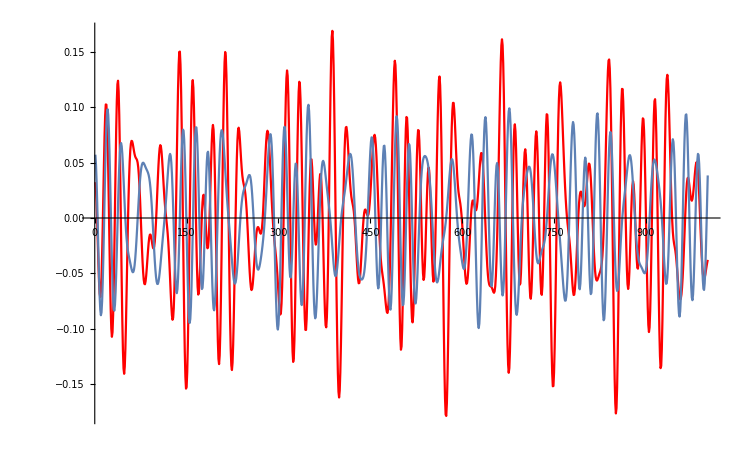

```mathematica
Show[ListLinePlot[Re[hscaledlistFC],PlotStyle->Red],ListLinePlot[Re[hscaledlistgeo]]]
```

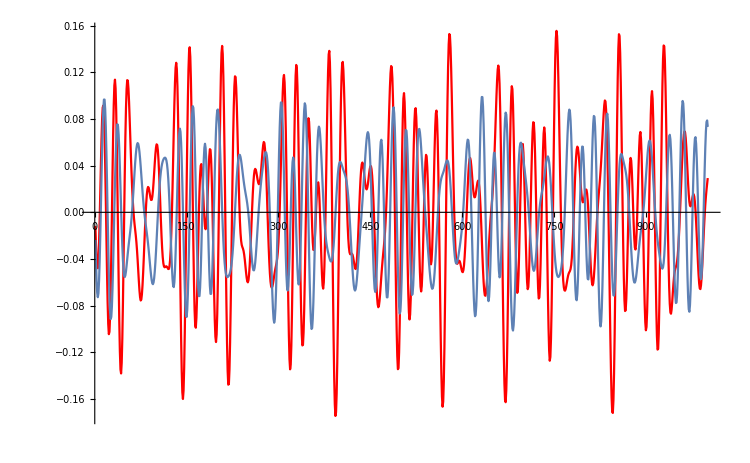

```mathematica
Show[ListLinePlot[Im[hscaledlistFC],PlotStyle->Red],ListLinePlot[Im[hscaledlistgeo]]]
```

### Computation amplitudes for fixed turning points

```mathematica
nmax=3;
kmax=3;
```

```mathematica
nvec=Table[n,{n,-nmax,nmax}];
kvec=Table[k,{k,-kmax,kmax}];
```

```mathematica
AbsoluteTiming[ampparDH=Table[TeukolskySpinModeCorrectionDH[2,2,n,k,corrDHparwaveform],{n,-nmax,nmax},{k,-kmax,kmax}];]
```

NDSolve::precw: The precision of the differential equation ({{TeukolskySpinFluxes`Private`X0$966062'[TeukolskySpinFluxes`Private`r$966062]==TeukolskySpinFluxes`Private`Y0$966062[TeukolskySpinFluxes`Private`r$966062],«6»,TeukolskySpinFluxes`Private`Y1$966062[78.93058852916284239743243763792948697224]==0.00001094342413000722067984036796828-0.00005540600945969257855432853059449 ⅈ},{},{},{},{}}) is less than WorkingPrecision (32.0377).

NDSolve::precw: The precision of the differential equation ({{TeukolskySpinFluxes`Private`X0$978980'[TeukolskySpinFluxes`Private`r$978980]==TeukolskySpinFluxes`Private`Y0$978980[TeukolskySpinFluxes`Private`r$978980],«6»,TeukolskySpinFluxes`Private`Y1$978980[68.43862079043574332468553451956427436459]==0.00001196887748811526524426063153061-0.00006127241708973308850880403188288 ⅈ},{},{},{},{}}) is less than WorkingPrecision (32.0524).

NDSolve::precw: The precision of the differential equation ({{TeukolskySpinFluxes`Private`X0$1007090'[TeukolskySpinFluxes`Private`r$1007090]==TeukolskySpinFluxes`Private`Y0$1007090[TeukolskySpinFluxes`Private`r$1007090],«6»,TeukolskySpinFluxes`Private`Y1$1007090[153.190535335604939976693709220187932304]==-3.76956736907206070780354915042×10^-6+0.00001886222219124412492135485339686 ⅈ},{},{},{},{}}) is less than WorkingPrecision (31.7444).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

{336.043,Null}

Same as the FC parametrization

```mathematica
AbsoluteTiming[amportPlus=Table[TeukolskySpinModeCorrectionOrtPlus[2,2,n,k,corrortwaveform]["AmplitudesCorrection"]["ℐ"],{n,-nmax,nmax},{k,-kmax,kmax}];]
```

{2182.77,Null}

```mathematica
AbsoluteTiming[amportMinus=Table[TeukolskySpinModeCorrectionOrtMinus[2,2,n,k,corrortwaveform]["AmplitudesCorrection"]["ℐ"],{n,-nmax,nmax},{k,-kmax,kmax}];]
```

{1970.49,Null}

```mathematica
θgen=π/2;
ϕgen=0;
qsub=1/20;
ϕs=45;
sparsub=Sin[ϕs*π/180];
sortsub=Cos[ϕs*π/180];
```

```mathematica
𝒜gDH=Table[SWSHg[agen,2,2,nvec[[n]],kvec[[k]],0,θgen]/ωg[2,nvec[[n]],kvec[[k]],0]^2 ampparDH[[n,k]]["Amplitudes"]["ℐ"],{n,2nmax+1},{k,2kmax+1}];
```

```mathematica
δ𝒜DHpar=Table[ampparDH[[n,k]]["AmplitudesCorrection"]["ℐ"] SWSHg[agen,2,2,nvec[[n]],kvec[[k]],0,θgen]/ωg[2,nvec[[n]],kvec[[k]],0]^2+δSWSHDH[agen,2,2,nvec[[n]],kvec[[k]],0,θgen]/ωg[2,nvec[[n]],kvec[[k]],0]^2 ampparDH[[n,k]]["Amplitudes"]["ℐ"]-(2ωsDH[2,nvec[[n]],kvec[[k]],0])/ωg[2,nvec[[n]],kvec[[k]],0] 𝒜gDH[[n,k]],{n,2nmax+1},{k,2kmax+1}];
```

Same as the FC parametrization

```mathematica
δ𝒜DHortplus=Table[amportPlus[[n,k]] SWSHg[agen,2,2,nvec[[n]],kvec[[k]],1,θgen]/ωg[2,nvec[[n]],kvec[[k]],1]^2,{n,2nmax+1},{k,2kmax+1}];
```

```mathematica
δ𝒜DHortminus=Table[amportMinus[[n,k]] SWSHg[agen,2,2,nvec[[n]],kvec[[k]],-1,θgen]/ωg[2,nvec[[n]],kvec[[k]],-1]^2,{n,2nmax+1},{k,2kmax+1}];
```

### Plots fixed turning points

```mathematica
hscaledDH[u_]:=Sum[q *sort*δ𝒜DHortplus[[n,k]]  Exp[-ⅈ (ωg[2,nvec[[n]],kvec[[k]],1]+q *spar*ωsDH[2,nvec[[n]],kvec[[k]],1] )u]+q *sort*δ𝒜DHortminus[[n,k]]  Exp[-ⅈ (ωg[2,nvec[[n]],kvec[[k]],-1]+q *spar*ωsDH[2,nvec[[n]],kvec[[k]],-1] )u]+(q *spar*δ𝒜DHpar[[n,k]]+𝒜gDH[[n,k]])Exp[-ⅈ (ωg[2,nvec[[n]],kvec[[k]],0]+q *spar*ωsDH[2,nvec[[n]],kvec[[k]],0])u],{n,2nmax+1},{k,2kmax+1}]/.q->qsub/.spar->sparsub/.sort->sortsub;
```

```mathematica
hscaledgeo[u_]:=Sum[𝒜gDH[[n,k]] Exp[-ⅈ (ωg[2,nvec[[n]],kvec[[k]],0])u],{n,2nmax+1},{k,2kmax+1}];
```

```mathematica
ulist=Table[u,{u,0,1000}];
```

```mathematica
AbsoluteTiming[hscaledlistDH=hscaledDH[ulist];]
```

{1.86423,Null}

```mathematica
AbsoluteTiming[hscaledlistgeo=hscaledgeo[ulist];]
```

{0.15998,Null}

```mathematica
exportHeaderDH={{"u","RehDH","RehDHgeo"}};
exportStrDH="DH_waveform_q"<>ToString[qsub//N]<>"_a"<>ToString[agen//N]<>"_p"<>ToString[pgen//N]<>"_e"<>ToString[egen//N]<>"_x"<>ToString[xgen//N]<>"_sangle"<>ToString[ϕs*π/180//N]<>".dat";
exportPlotTableDH=Table[{ulist[[i]]//N,Re[hscaledlistDH[[i]]]//N,Re[hscaledlistgeo[[i]]]//N},{i,Length[ulist]}];
Export[exportStrDH,Join[exportHeaderDH,exportPlotTableDH]]
```

DH_waveform_q0.05_a0.9_p4._e0.3_x0.707107_sangle0.785398.dat

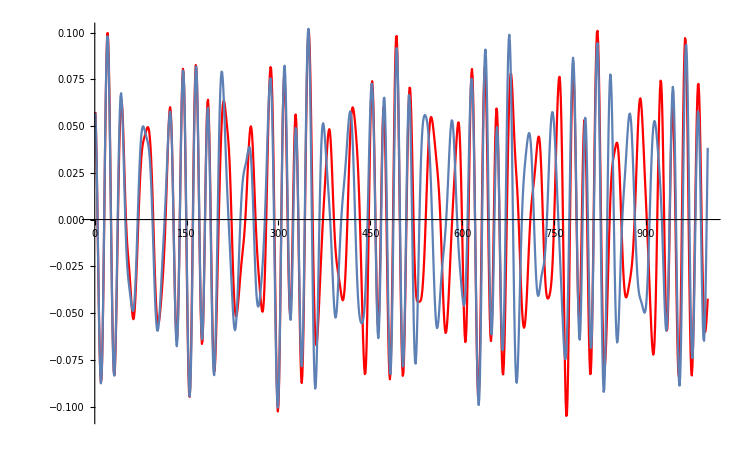

```mathematica
Show[ListLinePlot[Re[hscaledlistDH],PlotStyle->Red],ListLinePlot[Re[hscaledlistgeo]]]
```

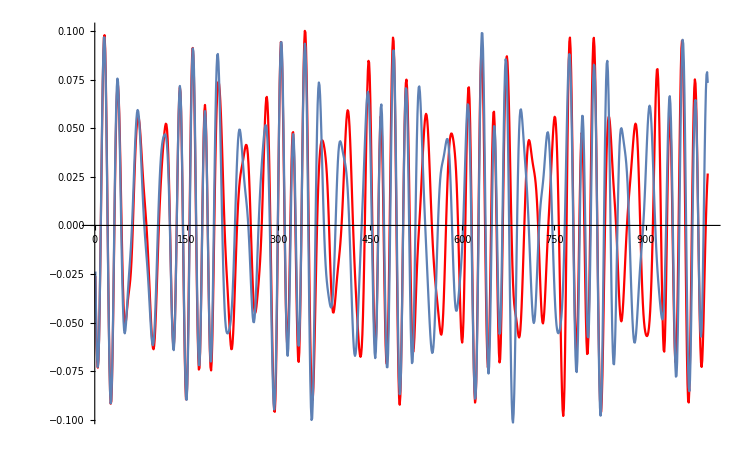

```mathematica
Show[ListLinePlot[Im[hscaledlistDH],PlotStyle->Red],ListLinePlot[Im[hscaledlistgeo]]]
```

## Convergence tests

### Loading all the necessary files

The package SpinOrbitsHamiltonJacobiNoChop is identical to SpinOrbitsHamiltonJacobi except for two things: the former does not include any Chop[... ,10^-16] functions in the sampling of the Fourier series (hence the name). The function Chop[... ,10^-16] set to zero any mode that is smaller than the threshold 10^-16. Moreover, SpinOrbitsHamiltonJacobiNoChop gives the Fourier coefficients of ξ_r and ξ_z.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
PacletDirectoryLoad["mod_SpinWeightedSpheroidalHarmonics2"];
```

```mathematica
<<SpinWeightedSpheroidalHarmonics`
<<KerrGeodesics`
<<Teukolsky`
```

```mathematica
Get["SpinOrbitsHamiltonJacobiNoChop.wl"]
```

```mathematica
Get["TeukolskySpinFluxesHamiltonJacobi.wl"]
```

### Test convergence ξ_r and ξ_z shifts functions vs nmax and kmax - fixed turning points

```mathematica
AbsoluteTiming[corrDHconvξe2=KerrSpinOrbitCorrectionDHPar[0.9`45,9`45,0.2`45,0.5`45,16,16];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{43.8287,Null}

```mathematica
AbsoluteTiming[corrDHconvξe4=KerrSpinOrbitCorrectionDHPar[0.9`45,9`45,0.4`45,0.5`45,16,16];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{46.014,Null}

```mathematica
AbsoluteTiming[corrDHconvξe6=KerrSpinOrbitCorrectionDHPar[0.9`45,9`45,0.6`45,0.5`45,16,16];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{45.0036,Null}

```mathematica
corrDHconvξe6["ξpar"][[1]][[;;,16+1]]//N
```

{1.90809×10^-21+0. ⅈ,-4.16723×10^-20+0. ⅈ,6.52329×10^-19+0. ⅈ,-6.18404×10^-18+0. ⅈ,-2.81267×10^-17+0. ⅈ,2.9387×10^-15+0. ⅈ,-8.08538×10^-14+0. ⅈ,1.49888×10^-12+0. ⅈ,-1.90633×10^-11+0. ⅈ,9.30346×10^-11+0. ⅈ,3.19182×10^-9+0. ⅈ,-1.14539×10^-7+0. ⅈ,2.3312×10^-6+0. ⅈ,-0.0000170541+0. ⅈ,0.000247385+0. ⅈ,0.0226986+0. ⅈ,0.0824507,0.0226986+0. ⅈ,0.000247385+0. ⅈ,-0.0000170541+0. ⅈ,2.3312×10^-6+0. ⅈ,-1.14539×10^-7+0. ⅈ,3.19182×10^-9+0. ⅈ,9.30346×10^-11+0. ⅈ,-1.90633×10^-11+0. ⅈ,1.49888×10^-12+0. ⅈ,-8.08538×10^-14+0. ⅈ,2.9387×10^-15+0. ⅈ,-2.81267×10^-17+0. ⅈ,-6.18404×10^-18+0. ⅈ,6.52329×10^-19+0. ⅈ,-4.16723×10^-20+0. ⅈ,1.90809×10^-21+0. ⅈ}

```mathematica
Abs[corrDHconvξe6["ξpar"][[1]][[;;,16+1]]]//N
```

{1.90809×10^-21,4.16723×10^-20,6.52329×10^-19,6.18404×10^-18,2.81267×10^-17,2.9387×10^-15,8.08538×10^-14,1.49888×10^-12,1.90633×10^-11,9.30346×10^-11,3.19182×10^-9,1.14539×10^-7,2.3312×10^-6,0.0000170541,0.000247385,0.0226986,0.0824507,0.0226986,0.000247385,0.0000170541,2.3312×10^-6,1.14539×10^-7,3.19182×10^-9,9.30346×10^-11,1.90633×10^-11,1.49888×10^-12,8.08538×10^-14,2.9387×10^-15,2.81267×10^-17,6.18404×10^-18,6.52329×10^-19,4.16723×10^-20,1.90809×10^-21}

```mathematica
Abs[corrDHconvξe6["ξpar"][[1]][[16+1,;;]]]//N
```

{7.21517×10^-19,0.,1.30999×10^-16,0.,2.35345×10^-14,0.,4.16757×10^-12,0.,7.22789×10^-10,0.,1.21327×10^-7,0.,0.000019209,0.,0.00265086,0.,0.0824507,0.,0.00265086,0.,0.000019209,0.,1.21327×10^-7,0.,7.22789×10^-10,0.,4.16757×10^-12,0.,2.35345×10^-14,0.,1.30999×10^-16,0.,7.21517×10^-19}

```mathematica
Abs[corrDHconvξe6["ξpar"][[1]][[;;,16+1]]]//N
```

{1.90809×10^-21,4.16723×10^-20,6.52329×10^-19,6.18404×10^-18,2.81267×10^-17,2.9387×10^-15,8.08538×10^-14,1.49888×10^-12,1.90633×10^-11,9.30346×10^-11,3.19182×10^-9,1.14539×10^-7,2.3312×10^-6,0.0000170541,0.000247385,0.0226986,0.0824507,0.0226986,0.000247385,0.0000170541,2.3312×10^-6,1.14539×10^-7,3.19182×10^-9,9.30346×10^-11,1.90633×10^-11,1.49888×10^-12,8.08538×10^-14,2.9387×10^-15,2.81267×10^-17,6.18404×10^-18,6.52329×10^-19,4.16723×10^-20,1.90809×10^-21}

```mathematica
Abs[corrDHconvξe6["ξpar"][[2]][[16+1,;;]]]//N
```

{3.63425×10^-19,0.,6.60612×10^-17,0.,1.18874×10^-14,0.,2.11004×10^-12,0.,3.67328×10^-10,0.,6.20895×10^-8,0.,9.97545×10^-6,0.,0.00148634,0.,0.0395174,0.,0.00148634,0.,9.97545×10^-6,0.,6.20895×10^-8,0.,3.67328×10^-10,0.,2.11004×10^-12,0.,1.18874×10^-14,0.,6.60612×10^-17,0.,3.63425×10^-19}

```mathematica
Abs[corrDHconvξe6["ξpar"][[2]][[;;,16+1]]]//N
```

{3.88092×10^-21,8.75457×10^-20,1.42107×10^-18,1.46445×10^-17,2.53774×10^-17,5.73963×10^-15,1.69503×10^-13,3.32167×10^-12,4.61115×10^-11,3.26283×10^-10,4.80316×10^-9,2.41083×10^-7,5.45603×10^-6,0.0000811211,0.000613006,0.00635387,0.0395174,0.00635387,0.000613006,0.0000811211,5.45603×10^-6,2.41083×10^-7,4.80316×10^-9,3.26283×10^-10,4.61115×10^-11,3.32167×10^-12,1.69503×10^-13,5.73963×10^-15,2.53774×10^-17,1.46445×10^-17,1.42107×10^-18,8.75457×10^-20,3.88092×10^-21}

```mathematica
exportHeaderDHconvnξr={{"n","ecc02","ecc04","ecc06"}};
exportHeaderDHconvkξr={{"k","ecc02","ecc04","ecc06"}};
exportStrDHconvnξr="xir_DH_conv_n"<>"_a"<>ToString[0.9//N]<>"_p"<>ToString[9//N]<>"_x"<>ToString[0.5//N]<>".dat";
exportStrDHconvkξr="xir_DH_conv_k"<>"_a"<>ToString[0.9//N]<>"_p"<>ToString[9//N]<>"_x"<>ToString[0.5//N]<>".dat";
```

```mathematica
nmax=16;
kmax=16;
nvec=Table[n,{n,-nmax,nmax}];
kvec=Table[k,{k,-kmax,kmax}];
```

```mathematica
exportPlotTableDHconvnξr=Table[{nvec[[n]],Abs[corrDHconvξe2["ξpar"][[1]][[n,16+1]]]//N,Abs[corrDHconvξe4["ξpar"][[1]][[n,16+1]]]//N,Abs[corrDHconvξe6["ξpar"][[1]][[n,16+1]]]//N},{n,1,2nmax+1}];
exportPlotTableDHconvkξr=Table[{kvec[[k]],Abs[corrDHconvξe2["ξpar"][[1]][[16+1,k]]]//N,Abs[corrDHconvξe4["ξpar"][[1]][[16+1,k]]]//N,Abs[corrDHconvξe6["ξpar"][[1]][[16+1,k]]]//N},{k,1,2kmax+1}];
```

```mathematica
Export[exportStrDHconvnξr,Join[exportHeaderDHconvnξr,exportPlotTableDHconvnξr],"Table",Alignment->Left]
Export[exportStrDHconvkξr,Join[exportHeaderDHconvkξr,exportPlotTableDHconvkξr],"Table",Alignment->Left]
```

xir_DH_conv_n_a0.9_p9._x0.5.dat

xir_DH_conv_k_a0.9_p9._x0.5.dat

### Test convergence ξ_r and ξ_z shifts functions - fixed constants of motion

```mathematica
AbsoluteTiming[corrFCconvξe2=KerrSpinOrbitCorrectionFCPar[0.9`45,9`45,0.2`45,0.5`45,16,16];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{44.6483,Null}

```mathematica
AbsoluteTiming[corrFCconvξe4=KerrSpinOrbitCorrectionFCPar[0.9`45,9`45,0.4`45,0.5`45,16,16];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{44.4528,Null}

```mathematica
AbsoluteTiming[corrFCconvξe6=KerrSpinOrbitCorrectionFCPar[0.9`45,9`45,0.6`45,0.5`45,16,16];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{44.5093,Null}

```mathematica
corrFCconvξe6["ξpar"][[1]][[;;,16+1]]//N
```

{1.90809×10^-21+0. ⅈ,-4.16723×10^-20+0. ⅈ,6.52329×10^-19+0. ⅈ,-6.18416×10^-18+0. ⅈ,-2.81279×10^-17+0. ⅈ,2.93805×10^-15+0. ⅈ,-8.08597×10^-14+0. ⅈ,1.49572×10^-12+0. ⅈ,-1.90918×10^-11+0. ⅈ,7.82892×10^-11+0. ⅈ,3.06379×10^-9+0. ⅈ,-1.77762×10^-7+0. ⅈ,1.81884×10^-6+0. ⅈ,-0.000244761+0. ⅈ,-0.0012904+0. ⅈ,-0.432997+0. ⅈ,-0.523021,-0.432997+0. ⅈ,-0.0012904+0. ⅈ,-0.000244761+0. ⅈ,1.81884×10^-6+0. ⅈ,-1.77762×10^-7+0. ⅈ,3.06379×10^-9+0. ⅈ,7.82892×10^-11+0. ⅈ,-1.90918×10^-11+0. ⅈ,1.49572×10^-12+0. ⅈ,-8.08597×10^-14+0. ⅈ,2.93805×10^-15+0. ⅈ,-2.81279×10^-17+0. ⅈ,-6.18416×10^-18+0. ⅈ,6.52329×10^-19+0. ⅈ,-4.16723×10^-20+0. ⅈ,1.90809×10^-21+0. ⅈ}

```mathematica
Abs[corrFCconvξe6["ξpar"][[1]][[;;,16+1]]]//N
```

{1.90809×10^-21,4.16723×10^-20,6.52329×10^-19,6.18416×10^-18,2.81279×10^-17,2.93805×10^-15,8.08597×10^-14,1.49572×10^-12,1.90918×10^-11,7.82892×10^-11,3.06379×10^-9,1.77762×10^-7,1.81884×10^-6,0.000244761,0.0012904,0.432997,0.523021,0.432997,0.0012904,0.000244761,1.81884×10^-6,1.77762×10^-7,3.06379×10^-9,7.82892×10^-11,1.90918×10^-11,1.49572×10^-12,8.08597×10^-14,2.93805×10^-15,2.81279×10^-17,6.18416×10^-18,6.52329×10^-19,4.16723×10^-20,1.90809×10^-21}

```mathematica
Abs[corrFCconvξe6["ξpar"][[1]][[16+1,;;]]]//N
```

{7.21517×10^-19,0.,1.30999×10^-16,0.,2.35345×10^-14,0.,4.16757×10^-12,0.,7.22789×10^-10,0.,1.21327×10^-7,0.,0.000019209,0.,0.00265086,0.,0.523021,0.,0.00265086,0.,0.000019209,0.,1.21327×10^-7,0.,7.22789×10^-10,0.,4.16757×10^-12,0.,2.35345×10^-14,0.,1.30999×10^-16,0.,7.21517×10^-19}

```mathematica
Abs[corrFCconvξe6["ξpar"][[1]][[;;,16+1]]]//N
```

{1.90809×10^-21,4.16723×10^-20,6.52329×10^-19,6.18416×10^-18,2.81279×10^-17,2.93805×10^-15,8.08597×10^-14,1.49572×10^-12,1.90918×10^-11,7.82892×10^-11,3.06379×10^-9,1.77762×10^-7,1.81884×10^-6,0.000244761,0.0012904,0.432997,0.523021,0.432997,0.0012904,0.000244761,1.81884×10^-6,1.77762×10^-7,3.06379×10^-9,7.82892×10^-11,1.90918×10^-11,1.49572×10^-12,8.08597×10^-14,2.93805×10^-15,2.81279×10^-17,6.18416×10^-18,6.52329×10^-19,4.16723×10^-20,1.90809×10^-21}

```mathematica
Abs[corrFCconvξe6["ξpar"][[2]][[16+1,;;]]]//N
```

{3.63425×10^-19,0.,6.60612×10^-17,0.,1.18874×10^-14,0.,2.11004×10^-12,0.,3.67333×10^-10,0.,6.20719×10^-8,0.,0.0000100342,0.,0.00133969,0.,0.301646,0.,0.00133969,0.,0.0000100342,0.,6.20719×10^-8,0.,3.67333×10^-10,0.,2.11004×10^-12,0.,1.18874×10^-14,0.,6.60612×10^-17,0.,3.63425×10^-19}

```mathematica
Abs[corrFCconvξe6["ξpar"][[2]][[;;,16+1]]]//N
```

{3.88092×10^-21,8.75457×10^-20,1.42107×10^-18,1.46445×10^-17,2.53774×10^-17,5.73963×10^-15,1.69503×10^-13,3.32167×10^-12,4.61115×10^-11,3.26283×10^-10,4.80316×10^-9,2.41083×10^-7,5.45603×10^-6,0.0000811211,0.000613006,0.00635387,0.301646,0.00635387,0.000613006,0.0000811211,5.45603×10^-6,2.41083×10^-7,4.80316×10^-9,3.26283×10^-10,4.61115×10^-11,3.32167×10^-12,1.69503×10^-13,5.73963×10^-15,2.53774×10^-17,1.46445×10^-17,1.42107×10^-18,8.75457×10^-20,3.88092×10^-21}

```mathematica
exportHeaderFCconvnξr={{"n","ecc0.2","ecc0.4","ecc0.6"}};
exportHeaderFCconvkξr={{"k","ecc0.2","ecc0.4","ecc0.6"}};
exportStrFCconvnξr="xir_FC_conv_n"<>"_a"<>ToString[0.9//N]<>"_p"<>ToString[9//N]<>"_x"<>ToString[0.5//N]<>".dat";
exportStrFCconvkξr="xir_FC_conv_k"<>"_a"<>ToString[0.9//N]<>"_p"<>ToString[9//N]<>"_x"<>ToString[0.5//N]<>".dat";
```

```mathematica
nmax=16;
kmax=16;
nvec=Table[n,{n,-nmax,nmax}];
kvec=Table[k,{k,-kmax,kmax}];
```

```mathematica
exportPlotTableFCconvnξr=Table[{nvec[[n]],Abs[corrFCconvξe2["ξpar"][[1]][[n,16+1]]]//N,Abs[corrFCconvξe4["ξpar"][[1]][[n,16+1]]]//N,Abs[corrFCconvξe6["ξpar"][[1]][[n,16+1]]]//N},{n,1,2nmax+1}];
exportPlotTableFCconvkξr=Table[{kvec[[k]],Abs[corrFCconvξe2["ξpar"][[1]][[16+1,k]]]//N,Abs[corrFCconvξe4["ξpar"][[1]][[16+1,k]]]//N,Abs[corrFCconvξe6["ξpar"][[1]][[16+1,k]]]//N},{k,1,2kmax+1}];
```

```mathematica
Export[exportStrFCconvnξr,Join[exportHeaderFCconvnξr,exportPlotTableFCconvnξr]]
Export[exportStrFCconvkξr,Join[exportHeaderFCconvkξr,exportPlotTableFCconvkξr]]
```

xir_FC_conv_n_a0.9_p9._x0.5.dat

xir_FC_conv_k_a0.9_p9._x0.5.dat

### Test convergence partial amplitudes vs nmax and kmax

```mathematica
AbsoluteTiming[corrDH4=KerrSpinOrbitCorrectionDHPar[0.9`65,9`65,0.5`65,0.5`65,4,4];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{0.587794,Null}

```mathematica
AbsoluteTiming[corrDH8=KerrSpinOrbitCorrectionDHPar[0.9`65,9`65,0.5`65,0.5`65,8,8];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{3.84797,Null}

```mathematica
AbsoluteTiming[corrDH12=KerrSpinOrbitCorrectionDHPar[0.9`65,9`65,0.5`65,0.5`65,12,12];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{14.2808,Null}

```mathematica
AbsoluteTiming[corrDH16=KerrSpinOrbitCorrectionDHPar[0.9`65,9`65,0.5`65,0.5`65,16,16];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{44.3251,Null}

```mathematica
nampmax=16;
kampmax=10;
```

```mathematica
AbsoluteTiming[ampDH4convk0=Table[Abs[TeukolskySpinModeCorrectionDH[2,2,n,0,corrDH4]["AmplitudesCorrection"]["ℐ"]],{n,0,nampmax}]//Quiet;]
```

{254.313,Null}

```mathematica
AbsoluteTiming[ampDH8convk0=Table[Abs[TeukolskySpinModeCorrectionDH[2,2,n,0,corrDH8]["AmplitudesCorrection"]["ℐ"]],{n,0,nampmax}]//Quiet;]
```

{352.162,Null}

```mathematica
AbsoluteTiming[ampDH12convk0=Table[Abs[TeukolskySpinModeCorrectionDH[2,2,n,0,corrDH12]["AmplitudesCorrection"]["ℐ"]],{n,0,nampmax}]//Quiet;]
```

{501.777,Null}

```mathematica
AbsoluteTiming[ampDH16convk0=Table[Abs[TeukolskySpinModeCorrectionDH[2,2,n,0,corrDH16]["AmplitudesCorrection"]["ℐ"]],{n,0,nampmax}]//Quiet;]
```

{706.55,Null}

```mathematica
exportHeaderFCconvampn={{"n","nmax4","nmax8","nmax16"}};
exportStrFCconvampn="corr_amp_DH_conv_n"<>"_a"<>ToString[0.9//N]<>"_p"<>ToString[9//N]<>"_e"<>ToString[0.5//N]<>"_x"<>ToString[0.5//N]<>".dat";
```

```mathematica
exportPlotTableFCconvampn=Table[{n-1,ampDH4convk0[[n]]//N,ampDH8convk0[[n]],ampDH16convk0[[n]]//N},{n,1,16+1}];
```

```mathematica
Export[exportStrFCconvampn,Join[exportHeaderFCconvampn,exportPlotTableFCconvampn]]
```

corr_amp_DH_conv_n_a0.9_p9._e0.5_x0.5.dat

```mathematica
AbsoluteTiming[ampDH4convn0=Table[Abs[TeukolskySpinModeCorrectionDH[2,2,0,k,corrDH4]["AmplitudesCorrection"]["ℐ"]],{k,-kampmax,kampmax}]//Quiet;]
```

{321.856,Null}

```mathematica
AbsoluteTiming[ampDH8convn0=Table[Abs[TeukolskySpinModeCorrectionDH[2,2,0,k,corrDH8]["AmplitudesCorrection"]["ℐ"]],{k,-kampmax,kampmax}]//Quiet;]
```

{433.196,Null}

```mathematica
AbsoluteTiming[ampDH12convn0=Table[Abs[TeukolskySpinModeCorrectionDH[2,2,0,k,corrDH12]["AmplitudesCorrection"]["ℐ"]],{k,-kampmax,kampmax}]//Quiet;]
```

{624.698,Null}

```mathematica
AbsoluteTiming[ampDH16convn0=Table[Abs[TeukolskySpinModeCorrectionDH[2,2,0,k,corrDH16]["AmplitudesCorrection"]["ℐ"]],{k,-kampmax,kampmax}]//Quiet;]
```

{936.483,Null}

```mathematica
kvecmax=Table[k,{k,-kampmax,kampmax}];
```

```mathematica
exportHeaderFCconvampk={{"k","kmax4","kmax12","kmax16"}};
exportStrFCconvampk="corr_amp_DH_conv_k"<>"_a"<>ToString[0.9//N]<>"_p"<>ToString[9//N]<>"_e"<>ToString[0.5//N]<>"_x"<>ToString[0.5//N]<>".dat";
```

```mathematica
exportPlotTableFCconvampk=Table[{kvecmax[[k]],ampDH4convn0[[k]]//N,ampDH12convn0[[k]],ampDH16convn0[[k]]//N},{k,2kampmax+1}];
```

```mathematica
Export[exportStrFCconvampk,Join[exportHeaderFCconvampk,exportPlotTableFCconvampk]]
```

corr_amp_DH_conv_k_a0.9_p9._e0.5_x0.5.dat

```mathematica
nvecmax=Table[n,{n,0,nampmax}];
```

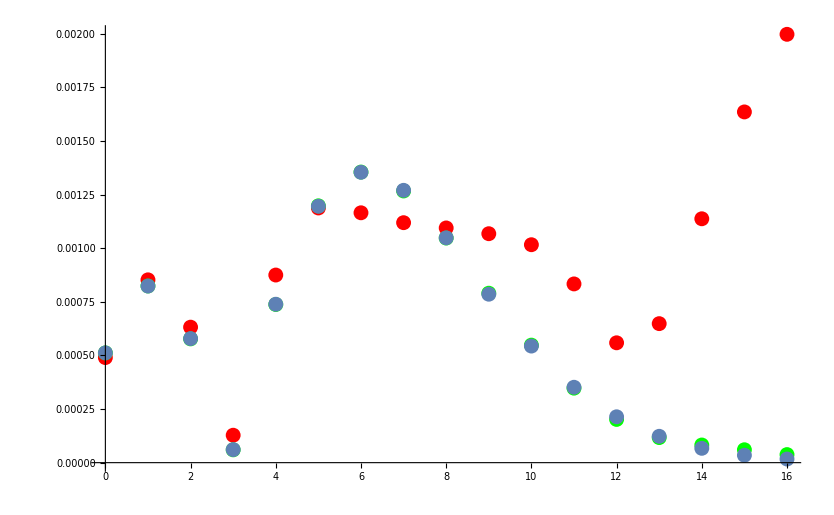

```mathematica
Show[{ListPlot[Table[{nvecmax[[n]],ampDH4convk0[[n]]},{n,nampmax+1}],PlotStyle->Red],ListPlot[Table[{nvecmax[[n]],ampDH8convk0[[n]]},{n,nampmax+1}],PlotStyle->Green],ListPlot[Table[{nvecmax[[n]],ampDH16convk0[[n]]},{n,nampmax+1}]]}]
```

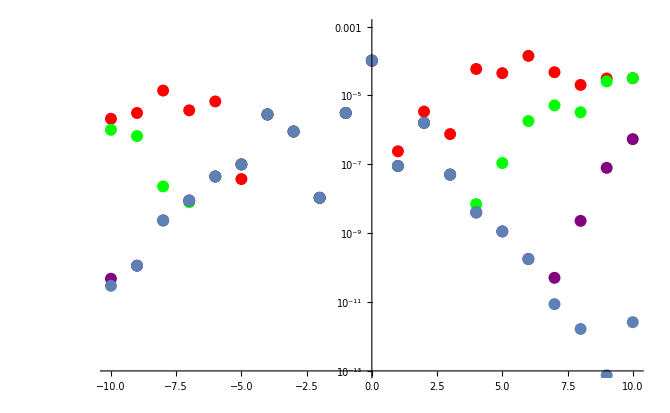

```mathematica
Show[{ListLogPlot[Table[{kvecmax[[n]],ampDH4convn0[[n]]},{n,2kampmax+1}],PlotStyle->Red,PlotRange->{Full,{10^-13,10^-3}}],ListLogPlot[Table[{kvecmax[[n]],ampDH8convn0[[n]]},{n,2kampmax+1}],PlotStyle->Green,PlotRange->{Full,{10^-13,10^-3}}],ListLogPlot[Table[{kvecmax[[n]],ampDH12convn0[[n]]},{n,2kampmax+1}],PlotStyle->Purple,PlotRange->{Full,{10^-13,10^-3}}],ListLogPlot[Table[{kvecmax[[n]],ampDH16convn0[[n]]},{n,2kampmax+1}],PlotRange->{Full,{10^-11,10^-1}}]}]
```

### Test convergence fluxes vs nmax and kmax

```mathematica
AbsoluteTiming[corrDH4=KerrSpinOrbitCorrectionDHPar[0.9`65,9`65,0.5`65,0.5`65,4,4];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{0.602833,Null}

```mathematica
AbsoluteTiming[corrDH8=KerrSpinOrbitCorrectionDHPar[0.9`65,9`65,0.5`65,0.5`65,8,8];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{3.82437,Null}

```mathematica
AbsoluteTiming[corrDH12=KerrSpinOrbitCorrectionDHPar[0.9`65,9`65,0.5`65,0.5`65,12,12];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{14.375,Null}

```mathematica
AbsoluteTiming[corrDH16=KerrSpinOrbitCorrectionDHPar[0.9`65,9`65,0.5`65,0.5`65,16,16];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{44.2183,Null}

```mathematica
AbsoluteTiming[fluxDH4conv=Table[TeukolskySpinModeCorrectionDH[2,2,n,k,corrDH4],{n,-3,3},{k,-3,3}]//Quiet;]
```

{439.638,Null}

```mathematica
AbsoluteTiming[fluxDH8conv=Table[TeukolskySpinModeCorrectionDH[2,2,n,k,corrDH8],{n,-3,3},{k,-3,3}]//Quiet;]
```

{502.768,Null}

```mathematica
AbsoluteTiming[fluxDH12conv=Table[TeukolskySpinModeCorrectionDH[2,2,n,k,corrDH12],{n,-3,3},{k,-3,3}]//Quiet;]
```

{641.69,Null}

```mathematica
AbsoluteTiming[fluxDH16conv=Table[TeukolskySpinModeCorrectionDH[2,2,n,k,corrDH16],{n,-3,3},{k,-3,3}]//Quiet;]
```

{829.938,Null}

```mathematica
fluxDH4convtot=Sum[fluxDH4conv[[n,k]]["FluxesCorrection"]["Energy"]["ℐ"]+fluxDH4conv[[n,k]]["FluxesCorrection"]["Energy"]["ℋ"],{n,2*3+1},{k,2*3+1}]
```

-7.9882991866917857523663433035134341134×10^-7

```mathematica
fluxDH8convtot=Sum[fluxDH8conv[[n,k]]["FluxesCorrection"]["Energy"]["ℐ"]+fluxDH8conv[[n,k]]["FluxesCorrection"]["Energy"]["ℋ"],{n,2*3+1},{k,2*3+1}]
```

-6.1495579228306953808806834732349747864×10^-7

```mathematica
fluxDH12convtot=Sum[fluxDH12conv[[n,k]]["FluxesCorrection"]["Energy"]["ℐ"]+fluxDH12conv[[n,k]]["FluxesCorrection"]["Energy"]["ℋ"],{n,2*3+1},{k,2*3+1}]
```

-6.1662609521261888945873332097299195262×10^-7

```mathematica
fluxDH16convtot=Sum[fluxDH16conv[[n,k]]["FluxesCorrection"]["Energy"]["ℐ"]+fluxDH16conv[[n,k]]["FluxesCorrection"]["Energy"]["ℋ"],{n,2*3+1},{k,2*3+1}]
```

-6.1663823856237718601658565658918185131×10^-7

```mathematica
(1-fluxDH4convtot/fluxDH16convtot)*100
```

-29.54595883180401429470392231315759485

```mathematica
(1-fluxDH8convtot/fluxDH16convtot)*100
```

0.2728417042754407373831058737535534

```mathematica
(1-fluxDH12convtot/fluxDH16convtot)*100
```

0.00196928263589481805373819423183516